```mathematica
t[y_]:={Rectangle[{-5,-1+y},{5,1+y}]}
f[y_]:={Rectangle[{-5,-1+y},{-0.5,1+y}],Rectangle[{0.5,-1+y},{5,1+y}]}
b[y_]:={t[y],f[y]};
sec[r_,{l_,m_,n_}]:={Join[b[r][[l+1]],b[r+3][[m+1]],b[r+6][[n+1]]]}
Show[Graphics[Rotate[sec[20,{1,1,0}],3Pi/4,{0,0}]],Graphics[Rotate[sec[20,{1,1,0}],Pi/4,{0,0}]],Graphics[sec[20,{1,1,0}]]]
```

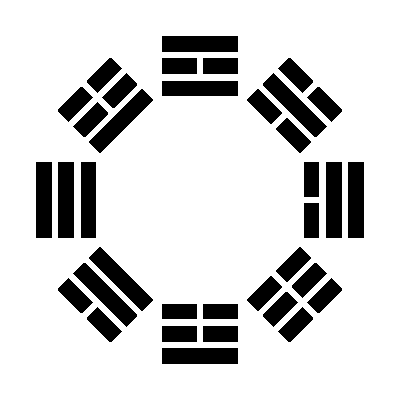

```mathematica
Show[Graphics[Rotate[sec[15,#[[1]]],#[[2]],{0,0}]]&/@Transpose@{Flatten[Table[{i,j,k},{i,0,1},{j,1,0,-1},{k,0,1}],2],Range[0,2Pi-Pi/4,Pi/4]}]
```

```mathematica
{Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2],Range[0,2Pi,Pi/4]}
```

{{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}},{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}}

```mathematica
BitXor[0,1]
```

1

```mathematica
l={{{0,0,0},0},{{1,1,1},-Pi},{{1,0,0},-Pi/4},{{0,1,1},-5Pi/4},{{1,0,1},-Pi/2},{{0,1,0},-3Pi/2},{{1,1,0},5Pi/4},{{0,0,1},-7Pi/4}};
c={{0,1},-{0,1},1/{√2,√2},-1/{√2,√2},{1,0},-{1,0},1/{√2,-√2},-1/{√2,-√2}};
lFold=FoldList[Append,{l[[1]]},l[[2;;]]];
cFold=FoldList[Append,{c[[1]]},c[[2;;]]];
series=Prepend[Table[Show[Graphics[{Rotate[sec[14,#[[1]]],#[[2]],{0,0}]&/@lFold[[i]],Thick,Blue,Arrow[12{{0,0},#}]&/@cFold[[i]]}],PlotRange->{{-25,25},{-25,25}},ImageSize->300],{i,Length[lFold]}],Graphics[{White,Circle[]},ImageSize->300]];
ListAnimate[series]
```

```mathematica
exp["resource/csEntry.gif",Magnify[#]&/@Join[Prepend[Reverse[series],series[[9]]],Append[series,series[[9]]]],1.2/5]
```

```mathematica
l={{{0,0,0},0},{{1,0,0},-Pi/4},{{1,0,1},-Pi/2},{{1,1,0},5Pi/4},{{1,1,1},-Pi},{{0,1,1},-5Pi/4},{{0,1,0},-3Pi/2},{{0,0,1},-7Pi/4}};
c={{0,1},1/{√2,√2},{1,0},1/{√2,-√2},-{0,1},-1/{√2,√2},-{1,0},-1/{√2,-√2}};
lFold=Join[Table[l[[1;;i]],{i,7}],Table[l[[i;;8]],{i,8}]];
cFold=Join[Table[c[[1;;i]],{i,7}],Table[c[[i;;8]],{i,8}]];
series=Prepend[Table[Show[Graphics[{Rotate[sec[14,#[[1]]],#[[2]],{0,0}]&/@lFold[[i]],Thick,Blue,Arrow[12{{0,0},#}]&/@cFold[[i]]}],PlotRange->{{-25,25},{-25,25}},ImageSize->300],{i,Length[lFold]}],Graphics[{White,Circle[]},ImageSize->300]];
ListAnimate[series]
```

```mathematica
exp["resource/csEntry.gif",Magnify[#]&/@series,2/5]
```

/Users/b2l/GitHub/borntoleave.github.io/resource/csEntry.gif

```mathematica
star[r_]:=Graphics[{Thick,Line[r{{0,1},-{0,1},1/{√2,√2},-1/{√2,√2},{1,0},-{1,0},1/{√2,-√2},-1/{√2,-√2},-{0,1},{0,1},-1/{√2,√2},1/{√2,√2},-{1,0},{1,0},-1/{√2,-√2},1/{√2,-√2},{0,1}}]}]
```

```mathematica
s=rs["ani/untitled.000"<>StringPadLeft[ToString[#],2,"0"]<>".ppm"]&/@Join[{3,3},Range[3,22]];
exp["resource/phyEntry.gif",Join[s,Reverse@s],1.2/11]
```

/Users/b2l/GitHub/borntoleave.github.io/resource/phyEntry.gif